```mathematica
Clear[coord,L,nPart,dt,dx,k,s,xPos,u0,myTemp,waveL,rightT,leftT,lastT,newT,newT];
(*Part A delta t= delta x/2*)
L:=1                                 (*Length of rod *)
nPart:=30                      (*Number of partitions *)
nTsamples:=1000         (*Number of time samples*)
tTime:=10                  (*How much time*)
dx:=L/nPart                         (*Section size Δx*)
dt:=dx/2      (*Time interval size Δt*)
c:=1                          (*k value*)
(*s=k*dt/(dx^2)*)                   (*s constant*)
s:=(c*dt/dx)
(*Interesting to note that forcing various *)
(*values on s affects the stability of the solution*)

(*Here I define a function for the initial temperature distribution f0=f(x)*)

f0[x_]:=Piecewise[{{0,x≥0&&x≤.25L},{1,x>0.25L&&x<0.75L},{0,x≥0.75L&&x≤L}}]

(*Here is where I define the initial conditions at t=0*)
(*so u(x,0)=the function f0=f(x) acting on the xpos*)
xPos:=(Range[nPart]-1)*dx;
AppendTo[xPos,dx*nPart];

(*the symbol /@ maps the function onto xpos*)
u0:=f0/@xPos;

(*Initialize the empty u temperature list, these are*)
(*our sample solution points*)
waveL:={};

(*At t=1 we have our u0 list of temps*)
waveL=Append[waveL,u0];

(*This nested for loop sequence calculates the temps at time*)
(*t by using the difference equation on page 226 of the book*)
(*this is also the same one we derived in class*)

(*The outer loop only starts at t=2 because at t=1 this is t0 with*)
(*initial temp of u0 which we append before the loop*)
For[t=2,t≤nTsamples,t++,

(*Initialize an empty temporary list*)
myTemp:={};

(*This loop is where we go throuh each x and calculate*)
(*u(x,t), where t is from the outer loop*)
For[k=1,k≤nPart+1,k++,
lastT=waveL[[t-1,k]];

If[t==2,llastT=0, llastT=waveL[[t-2,k]]];

(*if we are at start position x0 or in this case x1*)
If[k==1,rightT=0; leftT=waveL[[t-1,k+1]]];

(*if we reach the end of the rod*)
If[k==nPart+1,leftT=0;rightT=waveL[[t-1,k-1]]];

(*if we are inside rod*)
If[k>1&&k<nPart+1, 
rightT=waveL[[t-1,k-1]];
leftT=waveL[[t-1,k+1]]
];

(*This is the relationship: u[j][m+1]=u[j][m]...from page 226*)
newT=2lastT+s^2*(leftT-2*lastT+rightT)-llastT;

(*append temperatures to temporary list we started with*)
myTemp=Append[myTemp,newT];
];

(*append the temp list to our waveL list which we began before*)
(*the outer loop*)
waveL=Append[waveL,myTemp];
];
```

1/2

```mathematica
(*Here we define individual frames representing the solution*) (*at different times of t*)

(*Initialize an empty frame list, we will collect the frames*)
frames:={}

(*We need to get the coordinates of the xpos and waveL at*)
(*those xpos at time t here I accidentally used the letter k instead*)
For[k=1, k≤nTsamples,k++,
coord:={};

For[i=1,i≤nPart+1,i++,
coord=Append[coord,{xPos[[i]],waveL[[k,i]]}];
];

tempframe:=ListLinePlot[coord,PlotRange->{-nPart+1,nPart+1}];
frames=Append[frames,tempframe];
];

(*Try manipulating the plot*)
Manipulate[Show[frames[[n]]],{n,1,nTsamples,1}]
```

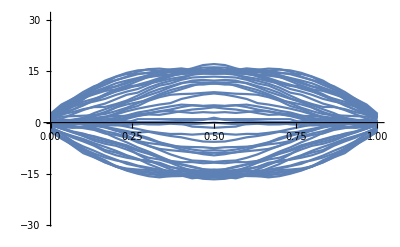

```mathematica
(*Here are the time snapshots of the vibration*)
myTablePlot:=Table[frames[[n]],{n,1,nTsamples,20}]
Show[myTablePlot]
(*Notice when dt = dx/2 the plots are stable*)
```

```mathematica
coord:={};
For[k=1, k≤nTsamples,k++,
For[i=1,i≤nPart+1,i++,
coord=Append[coord,{xPos[[i]],(k-1)*tTime/nTsamples,waveL[[k,i]]}];
];
];

ctPlot=ListContourPlot[coord,ColorFunction->"Rainbow"];
listPlot=ListPlot3D[coord,ColorFunction->"Rainbow",PlotRange->{-nPart,nPart}];

level=-nPart;gr=Graphics3D[{Texture[ctPlot],EdgeForm[],Polygon[{{0,0,level},{L,0,level},{L,tTime,level},{0,tTime,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->{{"Ambient", White}}];

Show[listPlot,gr,PlotRange->All,BoxRatios->{1, 1, 1}]
```

-Graphics3D-